```mathematica
(* constants*)
(*https://en.wikipedia.org/wiki/Avogadro_constant*)
N0=6.02214076*10^23;
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
me=9.10938291*10^(-28);
mev=0.510998928;
(*single monopole charge*)
Qm=2*Pi*hbar/e;
(*http://en.wikipedia.org/wiki/Fine-structure_constant*)
α=1/137.035999206;
αw=0.42541281596347497;
(*From:https://en.wikipedia.org/wiki/Fermi%27s_interaction*)
Gf=1.4327038609285911*^-49;
Ω=0.0078749969978123844;
kb=1.380658*10^(-16);
omega=0.00787499699;
mH=126*10^3*me/mev;
mp=1.672621777*10^(-24);
mn=1838.6402*me;
(*http://en.wikipedia.org/wiki/Weinberg_angle*)
θw0=0.231208;
θwrad=ArcSin[Sqrt[0.231208]];
θwdeg=θwrad*180/Pi;
(*https://en.wikipedia.org/wiki/Precision_tests_of_QED*)
g=2*1.00115965218085;
(* unification mass:anti-deSitter model*)
muni=3.6543166832631125*^-12;
mtau=1776.82*me/mev;
mmu=105.6583715*me/mev;
mpi=139.57018*me/mev;
mhiggs=126*10^3*me/mev;
mz=91.1876*10^3*me/mev;
mw=80.4335*10^3*me/mev;
mtop=172.76*10^3*me/mev;
mbottom=4.1*10^3*me/mev;
mcharm=1.275*10^3*me/mev;
mstrange=92.4*me/mev;
momegassb=6054.4/10^3;
mplanck=Sqrt[hbar*c/G];
mup=2.01*me/mev;
md0=4.79*me/mev;
(* log linear fit for 4th level quarks*)
mwhite=1.1677931388727855*^-19;
mblack=1.8611487827001873*^-22;
mout=1.5020666505936996*^-20;
Tvac=2.72548;
(*http://en.wikipedia.org/wiki/Observable_universe*)
ru=8.8*10^28/2;
rplanck=2*Pi*hbar/(mplanck*c);
tplanck=rplanck/c;
(*http://en.wikipedia.org/wiki/Big_Bang*)
(*years*days*hours*minutes*seconds*)
tu=13.798*10^9*365.25*24*60*60;
mnu=1.78266270 * 10^(-33 );
mnumu=6.7978246932973695*^-31;
mnutau=1.1431743145263108*^-29;
(*Weak charge on 5d simplex*)
Cw=(3!*2!)*Det[{{α,0,0,0,0,1},{0,α,0,0,0,1},{0,0,α,0,0,1},{0,0,0,α,0,1},{0,0,0,0,α,1},{0,0,0,0,0,1}}]/5!;
rw=Cw^2/(mnu*c^2);
(*http://www.bottomlayer.com/bottom/deutsch/neutrino.html*)
(* Weeks volume*)
vw=0.94270736277692772092;

(* Thurston-Meyerhoff volume*)
vt=0.981368828892232088914;
(*lepton hyperbolic 3 manifold volume*)
vl=(18/24)*vt;
pizero=134.9766*me/mev;
(* Bohr radius: https://en.wikipedia.org/wiki/Bohr_radius*)
ab=5.2917721067*10^(-9);
(*:https://en.wikipedia.org/wiki/Pion:*)
tpip=2.6033*10^(−8 );
tpiz=8.4*10^(−17);
(* product quarks masses in me*)
mup1=12.239779918021176;mdp1=12.256361761325056;
(* elliptic product quarks for Pi mesons*)
mupi=16.25229214603282;mdpi=16.805755043381577;
mqmu=Sqrt[mmu/me];
mqtau=Sqrt[mtau/me];
(* hadron strange and charm product quark masses*)
mqs=mqtau*mup1/mqmu;
mqc=2*mqs;
ttau=2.932*10^(−13);
tmu=2.1969811*10^(−6);
(*.10https://physicstoday.scitation.org/doi/10.1063/PT.3.4424*)
(*.10https://physics.stackexchange.com/questions/134856/units-of-hubble-time-and-hubble-constant*)
Hcbm=67.4/(3.09*10^19);
Hsnova=74.0/(3.09*10^19);
Hlense=73.3/(3.09*10^19);
Have=73.8/(3.09*10^19);
H0=2.2894835758225842*^-18;
th0=1/H0;
(* CMB age*)
tcmb=372000*365.25*24*60*60;
tsnova=1/Hsnova;
msun=1.9891*10^33;
(*first approximation electron g:single loop GED:weak g'*)
g0=2*(1+α/2);
Clear[g1]
g1=g1/.Solve[(g1/Sqrt[g+g1^2])^2==0.231208,g1][[2]];
(* gravity momemt γ*)
γ=e*G/(hbar*c);
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
(* anomalous magnetic moment of electron:https://en.wikipedia.org/wiki/Anomalous_magnetic_dipole_moment*)
ae=0.0015865218059;
```

```mathematica
m0=(mp*me*mn*mnu)^(1/4)
```

```mathematica
1.4604456445318845*^-27/me
```

1.60323

```mathematica
m0/(2*Pi*hbar)
```

```mathematica
0.2204088464082489/θw0
```

0.953292

```mathematica
mp0=mp/m0
```

1145.28

```mathematica
me0=me/m0
```

0.62374

```mathematica
mn0=mn/m0
```

1146.83

```mathematica
mnu0=mnu/m0
```

1.22063×10^-6

```mathematica
p[x_]=ExpandAll[(x-mp0)*(x-me0)*(x-I*mn0)*(x-I*mnu0)]
```

(-1.+0. ⅈ)+(1.60411-819250. ⅈ) x+(714.357+1.31416×10^6 ⅈ) x^2-(1145.91+1146.83 ⅈ) x^3+x^4

```mathematica
CoefficientList[p[x],x]
```

{-1.+0. ⅈ,1.60411-819250. ⅈ,714.357+1.31416×10^6 ⅈ,-1145.91-1146.83 ⅈ,1}

```mathematica
D[p[x],{x,1}]
```

(1.60411-819250. ⅈ)+(1428.71+2.62833×10^6 ⅈ) x-(3437.72+3440.5 ⅈ) x^2+4 x^3

```mathematica
Solve[D[p[x],{x,1}]==0,x]
```

{{x→0.311828+0.0000430155 ⅈ},{x→50.8655+809.445 ⅈ},{x→808.252+50.6802 ⅈ}}

```mathematica
w=p[x]/.Solve[D[p[x],{x,1}]==0,x]
```

{34.2261-127715. ⅈ,-1.75493×10^11-2.50062×10^11 ⅈ,-1.74606×10^11+2.49082×10^11 ⅈ}

```mathematica
(* neutron decay model:beta decay mechanism*)
```

```mathematica
(* p(+)+nu(0)<-Higgs+vacuum<-n(0)+e(+)*)
```

```mathematica
m0*{34.22613747492805-127714.88337169337 ⅈ,-1.7549303787906372*^11-2.5006170934283228*^11 ⅈ,-1.7460553454236578*^11+2.490819696673025*^11 ⅈ}
```

{4.99854×10^-26-1.86521×10^-22 ⅈ,-2.56298×10^-16-3.65202×10^-16 ⅈ,-2.55002×10^-16+3.63771×10^-16 ⅈ}

```mathematica
(*higgs as z0+Plus Pi*)
```

```mathematica
4.998541340440818*^-26/mpi
```

0.200901

```mathematica
1.865206451620872*^-22/mz
```

1.14742

```mathematica
(*vacuum level dual particle*)
```

```mathematica
Solve[(-2.5629804281614764*^-16-3.652015342739374*^-16 ⅈ)*m==2*Pi*hbar/c,m]
```

{{m→-2.84574×10^-22+4.05492×10^-22 ⅈ}}

```mathematica
m/mhiggs/.Solve[(-2.5629804281614764*^-16-3.652015342739374*^-16 ⅈ)*m==2*Pi*hbar/c,m]
```

```mathematica
Abs[{-1.266938695277385+1.805273072952122 ⅈ}]
```

{2.20548}

```mathematica
Table[m/.Solve[m^2/(4.600103653518404*^-43)==w[[i]],m],{i,3}]
```

```mathematica
Abs[{{-1.7141458025550503*^-19+1.7136864925115838*^-19 ⅈ,1.71414580255505*^-19-1.7136864925115838*^-19 ⅈ},{-1.7292101764821989*^-16+3.326113269507646*^-16 ⅈ,1.729210176482198*^-16-3.326113269507646*^-16 ⅈ},{-1.7263864616512407*^-16-3.3185005331778084*^-16 ⅈ,1.7263864616512402*^-16+3.3185005331778074*^-16 ⅈ}}]
```

{{2.42384×10^-19,2.42384×10^-19},{3.74876×10^-16,3.74876×10^-16},{3.7407×10^-16,3.7407×10^-16}}

```mathematica
Table[Solve[me^2/λ==w[[i]],λ],{i,3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{λ→1.74122×10^-63+6.49735×10^-60 ⅈ}},{{λ→-1.56035×10^-66+2.22336×10^-66 ⅈ}},{{λ→-1.56588×10^-66-2.23379×10^-66 ⅈ}}}

```mathematica
Table[Solve[mp^2/λ==w[[i]],λ],{i,3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{λ→5.87044×10^-57+2.19055×10^-53 ⅈ}},{{λ→-5.26066×10^-60+7.49597×10^-60 ⅈ}},{{λ→-5.2793×10^-60-7.53113×10^-60 ⅈ}}}

```mathematica
Table[Solve[mn^2/λ==w[[i]],λ],{i,3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{λ→5.88635×10^-57+2.19649×10^-53 ⅈ}},{{λ→-5.27492×10^-60+7.51629×10^-60 ⅈ}},{{λ→-5.29361×10^-60-7.55155×10^-60 ⅈ}}}

```mathematica
Table[Solve[mnu^2/λ==w[[i]],λ],{i,3}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{{λ→6.66827×10^-75+2.48827×10^-71 ⅈ}},{{λ→-5.97562×10^-78+8.51472×10^-78 ⅈ}},{{λ→-5.99679×10^-78-8.55467×10^-78 ⅈ}}}

```mathematica
(*Mexican hat plot*)
```

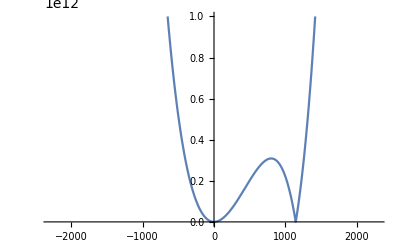

```mathematica
Plot[Abs[p[x]],{x,-2*mp0,2*mp0},PlotRange->{{-2*mp0,2*mp0},{0,10^12}},ImageSize->Full]
```

```mathematica
{-1,(me mn mnu mp)^(1/4)/me-(ⅈ (me mn mnu mp)^(1/4))/mn-(ⅈ (me mn mnu mp)^(1/4))/mnu+(me mn mnu mp)^(1/4)/mp,(ⅈ √(me mn mnu mp))/(me mn)+(ⅈ √(me mn mnu mp))/(me mnu)+(√(me mn mnu mp))/(mn mnu)-(√(me mn mnu mp))/(me mp)+(ⅈ √(me mn mnu mp))/(mn mp)+(ⅈ √(me mn mnu mp))/(mnu mp),-(me mn mnu mp)^(3/4)/(me mn mnu)-(ⅈ (me mn mnu mp)^(3/4))/(me mn mp)-(ⅈ (me mn mnu mp)^(3/4))/(me mnu mp)-(me mn mnu mp)^(3/4)/(mn mnu mp),1}
```

{-1,1.60411-819250. ⅈ,714.357+1.31416×10^6 ⅈ,-1145.91-1146.83 ⅈ,1}

```mathematica
-1+((me mn mnu mp)^(1/4) x)/me-(ⅈ (me mn mnu mp)^(1/4) x)/mn-(ⅈ (me mn mnu mp)^(1/4) x)/mnu+((me mn mnu mp)^(1/4) x)/mp+(ⅈ √(me mn mnu mp) x^2)/(me mn)+(ⅈ √(me mn mnu mp) x^2)/(me mnu)+(√(me mn mnu mp) x^2)/(mn mnu)-(√(me mn mnu mp) x^2)/(me mp)+(ⅈ √(me mn mnu mp) x^2)/(mn mp)+(ⅈ √(me mn mnu mp) x^2)/(mnu mp)-((me mn mnu mp)^(3/4) x^3)/(me mn mnu)-(ⅈ (me mn mnu mp)^(3/4) x^3)/(me mn mp)-(ⅈ (me mn mnu mp)^(3/4) x^3)/(me mnu mp)-((me mn mnu mp)^(3/4) x^3)/(mn mnu mp)+x^4
```

-1+(1.60411-819250. ⅈ) x+(714.357+1.31416×10^6 ⅈ) x^2-(1145.91+1146.83 ⅈ) x^3+x^4

```mathematica
1/(me mn mnu mp)(-me mn mnu mp+me mn mnu (me mn mnu mp)^(1/4) x-ⅈ me mn mp (me mn mnu mp)^(1/4) x-ⅈ me mnu mp (me mn mnu mp)^(1/4) x+mn mnu mp (me mn mnu mp)^(1/4) x+ⅈ me mn √(me mn mnu mp) x^2+ⅈ me mnu √(me mn mnu mp) x^2-mn mnu √(me mn mnu mp) x^2+me mp √(me mn mnu mp) x^2+ⅈ mn mp √(me mn mnu mp) x^2+ⅈ mnu mp √(me mn mnu mp) x^2-me (me mn mnu mp)^(3/4) x^3-ⅈ mn (me mn mnu mp)^(3/4) x^3-ⅈ mnu (me mn mnu mp)^(3/4) x^3-mp (me mn mnu mp)^(3/4) x^3+me mn mnu mp x^4)
```

2.19816×10^107 (-4.54927×10^-108+(7.29751×10^-108-3.72699×10^-102 ⅈ) x+(3.2498×10^-105+5.97848×10^-102 ⅈ) x^2-(5.21303×10^-105+5.21725×10^-105 ⅈ) x^3+4.54927×10^-108 x^4)

```mathematica
ComplexPlot[p[x],{x,-2*mp0-I*2*mn0,2*mp0+I*2*mn0},ColorFunction->"CyclicReImLogAbs",ImageSize->Full]
```

-Graphics-